```mathematica
(* il nuovo codice è scritto usando la condizione che 1==1 nell'integrale e usando le nuove funzioni δψ *)
```

```mathematica
(*******************************)(*******************************)(*******************************)(*******************************)(*******************************)(*******************************)(*******************************)(*******************************)(*******************************)(*******************************)(*******************************)
(* Prova che l'integrale vale uno *)
```

```mathematica
(** parametri equazioni *)
m=2;

dtt=0.08; (* dt target *)

(* parametri soluzione numerica *)

(* NN=100; *) 

Lm=20;
LM=10;

NN=IntegerPart[Lm/dtt] (* prendo NN in modo da avviciarmi al dt target *)

dt=Lm/NN; (* fondamentale deve essere un razionale, altrimenti non funziona come indici !!!! *)
N[dt]

H=N[E^-Lm]
J=.01;


(* condizione iniziale *)
Do[nψ[tt]= E^(H/(m-1))Chop[E^(- E^tt)],{tt,-Lm,LM,dt}];

(* condizione iniziale costante *)
(*
Do[nψ[tt]= E^(H/(m-1))1.,{tt,-Lm,LM,dt}];
Do[nψ[tt]= 0.,{tt,-Lm,LM,dt}];
*)
Do[ψ[t]=nψ[t];,{t,-Lm,LM,dt}];
```

250

0.08

2.06115×10^-9

```mathematica
nψ[-Lm]=   1.;
Do[
int=0;
int=95/288 1/2 E^J  (1-H^2 E^(-2 t))( J E^t/H)^2 Exp[-J  E^t/H];
(* questo è il contributo all'integrale che viene da tt=-Lm, è moltiplicato per 281/720, per ricavarlo si usa il limite della Bessel per argomento nullo, dall'altra parte invece non dovrei avere problemi *)

tt=-Lm+dt;

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=317/240(J^(1/2)E^J)/(2 π)^(1/2) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* questo è il contributo all'integrale che viene da tt=-Lm+dt, è moltiplicato per 1057/720 *)

tt=-Lm+2dt;

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=23/30(J^(1/2)E^J)/(2 π)^(1/2) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* questo è il contributo all'integrale che viene da tt=-Lm+2 , è moltiplicato per ...  *)
tt=.;


tt=-Lm+3dt;

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=793/720(J^(1/2)E^J)/(2 π)^(1/2) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* questo è il contributo all'integrale che viene da tt=-Lm+3 , è moltiplicato per ...  *)
tt=.;


tt=-Lm+4dt;

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=157/160(J^(1/2)E^J)/(2 π)^(1/2) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* questo è il contributo all'integrale che viene da tt=-Lm+4 , è moltiplicato per ...  *)
tt=.;





Do[

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=(J^(1/2)E^J)/(2 π)^(1/2) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2 tende a zero per x che diverge, cioe' H piccolo *)
,{tt,-Lm+5dt,LM,dt}];
nψ[t]=   Exp[J-J E^t/H]+   int dt;,{t,-Lm+dt,LM,dt}];
```

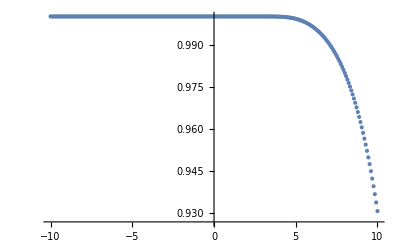

```mathematica
ListPlot[Table[{t,N[nψ[t]]},{t,-Lm,LM,dt}],PlotRange->All]
```

```mathematica
s20=Table[{t+Lm,N[nψ[t]]-1},{t,-Lm,LM,dt}];
```

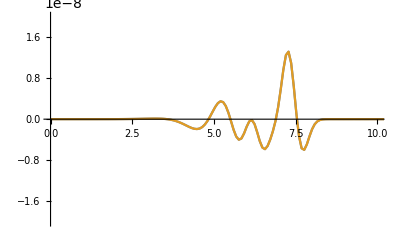

```mathematica
ListPlot[{s10,s20},PlotRange->{{0,10},{-2 10^-8,2 10^-8}},Joined->True]
```

```mathematica
(*******************************)(*******************************)(*******************************)(*******************************)(*******************************)(*******************************)(*******************************)(*******************************)(*******************************)(*******************************)(*******************************)
```

```mathematica
(***************************************************)
(***************************************************)
(***************************************************)
(***************************************************)
(***************************************************)
(***************************************************)

(* definizione *)
```

```mathematica
(*   (1-deltaψ[tt] E^(b tt))= ψ[tt] *)
```

```mathematica
m=2
```

2

```mathematica
Expand[E^(-b t)(1-ψ[tt]^m E^(-E^tt) )/.{ψ[tt]->(1-deltaψ[tt] E^(b tt))}]
```

ⅇ^(-b t)-ⅇ^(-ⅇ^tt-b t)+2 ⅇ^(-ⅇ^tt-b t+b tt) deltaψ[tt]-ⅇ^(-ⅇ^tt-b t+2 b tt) deltaψ[tt]^2

```mathematica
ⅇ^(-b t)(1-ⅇ^(-ⅇ^tt))+2 ⅇ^(-ⅇ^tt-b t+b tt) deltaψ[tt]-ⅇ^(-ⅇ^tt-b t+2 b tt) deltaψ[tt]^2

(ⅇ^(-b t)2 E^(-ⅇ^tt/2) Sinh[ⅇ^tt/2]+2 ⅇ^(-ⅇ^tt-b t+b tt) deltaψ[tt]-ⅇ^(-ⅇ^tt-b t+2 b tt) deltaψ[tt]^2)
```

```mathematica
(***************************************************)
(***************************************************)
(***************************************************)
(***************************************************)
(***************************************************)
(***************************************************)
```

```mathematica
(* NUOVO CODICE *)
```

```mathematica
(** parametri equazioni *)
m=2; (* !!!!!!!!!!!!!!! ATTENZIONE IL CODICE VALE SOLO PER m=2, altrimenti bisogna cambiare l'espressione *)

dtt=0.08; (* dt target *)

(* parametri soluzione numerica *)

(* NN=100; *) 

Lm=14;
LM=10;

NN=IntegerPart[Lm/dtt] ;(* prendo NN in modo da avviciarmi al dt target *)

dt=Lm/NN; (* fondamentale deve essere un razionale, altrimenti non funziona come indici !!!! *)
N[dt]

H=N[E^-Lm]
J=0.026540159736761493;  (* valore critico *)
b=.5;


(* condizione iniziale, inizializzata con una soluzione già trovata *)
Do[nψ[tt]= Interpolation[lisψ14p08cri][tt],{tt,-Lm,LM,dt}];
Do[ndeltaψ[tt]= (1-nψ[tt])E^(-b tt),{tt,-Lm,LM,dt}];


(* la condizione iniziale nel caso di nuovi punti la possiamo fare prendendo la soluzione con H=0, calcoliamo la su deltaψ che sarà costante e uguale a c per t negativi. Poi prendiamo questa soluzione e la moltiplichiamo per (1-t/Subscript[t, min]) per t negativi, dovrebbe essere un buon punto di partenza per l'iterazione *)


Do[ψ[t]=nψ[t];,{t,-Lm,LM,dt}];
Do[deltaψ[t]=(1-ψ[t])E^(-b t);,{t,-Lm,LM,dt}];
```

0.08

8.31529×10^-7

```mathematica
(** plot di deltapsi ottenuti dai vecchi codici e della condizione iniziale **)
```

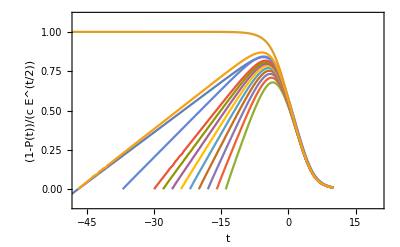

```mathematica
c=0.67573;b=.5;
Show[ListPlot[{Map[{#[[1]],(1-#[[2]])E^(-.5 #[[1]])/c (1-#[[1]]/(-47))}&,lisψ0crit],Map[{#[[1]],(1-#[[2]])E^(-.5 #[[1]])/c}&,lisψ0crit],Map[{#[[1]],(1-#[[2]])E^(-.5 #[[1]])/c}&,lisψ14p08cri],Map[{#[[1]],(1-#[[2]])E^(-.5 #[[1]])/c}&,lisψ16p08cri],Map[{#[[1]],(1-#[[2]])E^(-.5 #[[1]])/c}&,lisψ18p08cri],Map[{#[[1]],(1-#[[2]])E^(-.5 #[[1]])/c}&,lisψ20p08cri],Map[{#[[1]],(1-#[[2]])E^(-.5 #[[1]])/c}&,lisψ22p08cri],Map[{#[[1]],(1-#[[2]])E^(-.5 #[[1]])/c}&,lisψ24p08cri],Map[{#[[1]],(1-#[[2]])E^(-.5 #[[1]])/c}&,lisψ26p08cri],Map[{#[[1]],(1-#[[2]])E^(-.5 #[[1]])/c}&,lisψ28p08cri],Map[{#[[1]],(1-#[[2]])E^(-.5 #[[1]])/c}&,lisψ30p08cri],Map[{#[[1]],(1-#[[2]])E^(-.5 #[[1]])/c}&,lisψ37p02cri],Map[{#[[1]],(1-#[[2]])E^(-.5 #[[1]])/c}&,lisψ47p02cri]},PlotRange->{{-47,20},{-.1,1.1}},Joined->True,Frame->True,FrameLabel->{Style["t",Italic],Style["(1-P(t))/(c E^(t/2))",Italic]}]]
```

```mathematica
(* prova che il codice è buono *)
```

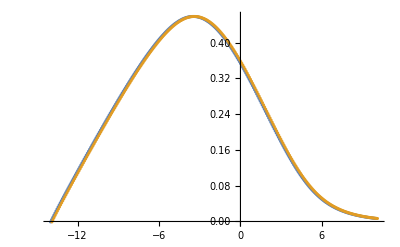

```mathematica
ListPlot[{Table[{t,ndeltaψ[t]},{t,-Lm,LM,dt}],Table[{t+.1,deltaψ[t]},{t,-Lm,LM,dt}]}]
```

```mathematica
IteraSolve:=(
Pite={};
dsol={};
dmaxite={};
dmax=1.;
While[dmax>10^-10,



(****************************************)
(* nuova parte di codice per t negativi *)
(****************************************)(****************************************)(****************************************)(****************************************)(****************************************)

ndeltaψ[-Lm]=2 H^-b E^(H/(-1+m)/2)Sinh[-H/(-1+m)/2]; 
nψ[-Lm]=E^(H/(-1+m));
(* ndeltaψ[-Lm]= E^(b Lm) (1- E^(H/(-1+m))); *)
Do[
int=0;
int=95/288 1/2 E^J ndeltaψ[-Lm] (1-H^2 E^(-2 t))( J E^t/H)^2 Exp[-J  E^t/H];


(* questo è il contributo all'integrale che viene da tt=-Lm, è moltiplicato per 281/720, per ricavarlo si usa il limite della Bessel per argomento nullo, dall'altra parte invece non dovrei avere problemi *)

tt=-Lm+dt;

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=317/240(J^(1/2)E^J)/(2 π)^(1/2)(ⅇ^(-b t)2 E^(-ⅇ^tt/2) Sinh[ⅇ^tt/2]+2 ⅇ^(-ⅇ^tt-b t+b tt) deltaψ[tt]-ⅇ^(-ⅇ^tt-b t+2 b tt) deltaψ[tt]^2)(1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* questo è il contributo all'integrale che viene da tt=-Lm+dt, è moltiplicato per 1057/720 *)

tt=-Lm+2dt;

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=23/30(J^(1/2)E^J)/(2 π)^(1/2)(ⅇ^(-b t)2 E^(-ⅇ^tt/2) Sinh[ⅇ^tt/2]+2 ⅇ^(-ⅇ^tt-b t+b tt) deltaψ[tt]-ⅇ^(-ⅇ^tt-b t+2 b tt) deltaψ[tt]^2) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* questo è il contributo all'integrale che viene da tt=-Lm+2 , è moltiplicato per ...  *)
tt=.;


tt=-Lm+3dt;

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=793/720(J^(1/2)E^J)/(2 π)^(1/2)(ⅇ^(-b t)2 E^(-ⅇ^tt/2) Sinh[ⅇ^tt/2]+2 ⅇ^(-ⅇ^tt-b t+b tt) deltaψ[tt]-ⅇ^(-ⅇ^tt-b t+2 b tt) deltaψ[tt]^2) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* questo è il contributo all'integrale che viene da tt=-Lm+3 , è moltiplicato per ...  *)
tt=.;


tt=-Lm+4dt;

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=157/160(J^(1/2)E^J)/(2 π)^(1/2)(ⅇ^(-b t)2 E^(-ⅇ^tt/2) Sinh[ⅇ^tt/2]+2 ⅇ^(-ⅇ^tt-b t+b tt) deltaψ[tt]-ⅇ^(-ⅇ^tt-b t+2 b tt) deltaψ[tt]^2) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* questo è il contributo all'integrale che viene da tt=-Lm+4 , è moltiplicato per ...  *)
tt=.;





Do[

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=(J^(1/2)E^J)/(2 π)^(1/2)(ⅇ^(-b t)2 E^(-ⅇ^tt/2) Sinh[ⅇ^tt/2]+2 ⅇ^(-ⅇ^tt-b t+b tt) deltaψ[tt]-ⅇ^(-ⅇ^tt-b t+2 b tt) deltaψ[tt]^2)(1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2 tende a zero per x che diverge, cioe' H piccolo *)
,{tt,-Lm+5dt,LM,dt}];
ndeltaψ[t]=   Exp[J-J E^t/H] E^(-b t)2  E^(H/(-1+m)/2)Sinh[-H/(-1+m)/2]+   int dt;
nψ[t]=1-E^(b t)ndeltaψ[t],{t,-Lm+dt,0,dt}];


(****************************************)
(* vecchia parte di codice per t negativi *)
(****************************************)(****************************************)(****************************************)(****************************************)(****************************************)




(* nψ[-Lm]=   E^(H/(-1+m));  questo l'abbiamo calcolato prima *)
Do[
int=0;
int=95/288 1/2 E^J E^(H/(-1+m))  (1-H^2 E^(-2 t))( J E^t/H)^2 Exp[-J  E^t/H];
(* questo è il contributo all'integrale che viene da tt=-Lm, è moltiplicato per 281/720, per ricavarlo si usa il limite della Bessel per argomento nullo, dall'altra parte invece non dovrei avere problemi *)

tt=-Lm+dt;

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=317/240(J^(1/2)E^J)/(2 π)^(1/2)ψ[tt]^m E^(-E^tt) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* questo è il contributo all'integrale che viene da tt=-Lm+dt, è moltiplicato per 1057/720 *)

tt=-Lm+2dt;

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=23/30(J^(1/2)E^J)/(2 π)^(1/2)ψ[tt]^m E^(-E^tt) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* questo è il contributo all'integrale che viene da tt=-Lm+2 , è moltiplicato per ...  *)
tt=.;


tt=-Lm+3dt;

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=793/720(J^(1/2)E^J)/(2 π)^(1/2)ψ[tt]^m E^(-E^tt) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* questo è il contributo all'integrale che viene da tt=-Lm+3 , è moltiplicato per ...  *)
tt=.;


tt=-Lm+4dt;

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=157/160(J^(1/2)E^J)/(2 π)^(1/2)ψ[tt]^m E^(-E^tt) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* questo è il contributo all'integrale che viene da tt=-Lm+4 , è moltiplicato per ...  *)
tt=.;





Do[

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=(J^(1/2)E^J)/(2 π)^(1/2)ψ[tt]^m E^(-E^tt) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2 tende a zero per x che diverge, cioe' H piccolo *)
,{tt,-Lm+5dt,LM,dt}];
nψ[t]=   Exp[J-J E^t/H] E^(H/(-1+m))+   int dt;
ndeltaψ[t]=(1-nψ[t])E^(-b t);
,{t,dt,LM,dt}];
 

(*************************)
(*************************)(*************************)(*************************)(*************************)(*************************)(*************************)(*************************)(*************************)

Do[diffψ[t]=ψ[t]-nψ[t];,{t,-Lm,LM,dt}];


dmax=Max[Table[Abs[diffψ[t]],{t,-Lm,LM,dt}]];
AppendTo[dsol,Table[{tt,diffψ[tt]/dmax},{tt,-Lm,LM,dt}]];
AppendTo[dmaxite,dmax];

Do[ψ[t]=nψ[t];,{t,-Lm,LM,dt}];
Do[deltaψ[t]=ndeltaψ[t];,{t,-Lm,LM,dt}];


P=0;
Do[P+=ψ[t]^(m+1) E^(- E^t) E^t ,{t,-Lm,LM,dt}];
P*=(dt); (* controllare la formula, manca un pezzo che dovrebbe dare correzioni regolari in H  *)
AppendTo[Pite,P];


])
```

```mathematica
IteraSolve[]
```

Null[]

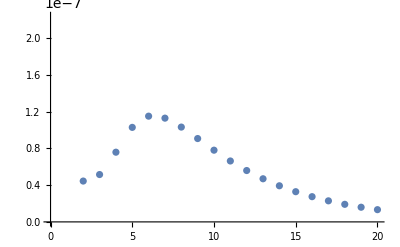

```mathematica
ListPlot[dmaxite]
```

```mathematica
(** parti da aggiungere dopo **)
```